```mathematica
If[StringTake[$SystemID,3]=="Win",
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\AvoidedQP\\implementation\\"],
SetDirectory["~/Documents/GitHub/AvoidedQP/reimplementation/"]
]
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/reimplementation

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
```

```mathematica
getAssoc[head_,JRange_,tail_]:=(
result={};
Do[(
file=StringJoin[head,"_1.0_",J,"_",tail,".json"];
qpData=Import[StringJoin["data/", file],"RawJSON"];
result=Join[result,qpData];
),{J,JRange}];
result
)
```

```mathematica
getStruct[ds_]:=(
sizeAvail=Normal[DeleteDuplicates[ds[Take,"size"]]];
momentumAvail= Normal[DeleteDuplicates[ds[Take,"momentum"]]];
interactionAvail=Normal[DeleteDuplicates[ds[Take,"interaction"]]];
couplingAvail=Normal[DeleteDuplicates[ds[Take,"coupling"]]];
hoppingAvail=Normal[DeleteDuplicates[ds[Take,"hopping"]]];
<|"size"->sizeAvail,"momentum"->momentumAvail,"interaction"->interactionAvail,"coupling" ->couplingAvail, "hopping"->hoppingAvail|>
)
```

```mathematica
extractData[ds_,directive_,keys_,invX_ :True]:=(
data=Apply[ds,directive];
x=(data[Take,keys[[1]]]//Normal);
y=(data[Take,keys[[2]]]//Normal);
If[invX,x=1/x];
result=Table[{x[[it]],y[[it]]},{it,Length[x]}];
Clear[x,y];
result
)
```

```mathematica
makeFits[data_,func_,arg_,points_]:=Table[Fit[d[[-Min[points,Length[d]];;-1]],func,arg],{d, data}];
```

```mathematica
getPlot[data_,func_, arg_,points_]:=(
SetOptions[LinTicks,TickLengthScale->2.5];

colors={Blue,Red};
pltStyle=Table[Directive[color,Opacity[0.7]],{color,colors}];
fpltStyle=Table[Directive[Dashed,color,Opacity[0.7]],{color,colors}];

plt=ListPlot[data,
PlotRange->{{0,0.1},{0,0.8}},ImageSize->240,
Frame->True,Axes->False,
FrameStyle->Directive[Black,18,FontFamily->"Bookman Old Style"],
PlotMarkers->{"●", 10},
PlotLegends->Placed[PointLegend[
Table[
Style[StringJoin["λ = ",ToString[NumberForm[B,{2,1}]]],16,FontFamily->"BookmanOldStyle"],
{B,qpAvail["interaction"]//Normal}],LegendLayout->"Column",Spacings->0.2],
{0.75,0.8}],
Epilog->Text[
Style["(a)  p = 0",Black,18,FontFamily->"Bookman Old Style"],
{0.025,0.8*(8.9/10)}],
FrameLabel->{(*Style["L^-1",Black,18,FontFamily->"Bookman Old Style"]*)None,Style["ΔE / t",Black,18,FontFamily->"Bookman Old Style"]},
LabelStyle->Directive[Black,18],
PlotStyle->pltStyle,
AspectRatio->.75,
FrameTicks->{{LinTicks[0,0.8,0.2,10],StripTickLabels[LinTicks[0,0.8,0.2,10]]},{LinTicks[0,0.1,0.05,10],StripTickLabels[LinTicks[0,0.1,0.05,10]]}}
];

fits=makeFits[data,func,arg,points];
fplt=Plot[fits,{x,0,1/10},PlotStyle->fpltStyle];

Show[plt,fplt,PlotRangeClipping->True]
)
```

```mathematica
makePlotsGapL[]:=(
fitFunctions={1,x(*,x/Log[1/x]*)};
fitPoints=5;

directive={Select[#coupling==J&&#momentum==k&&#interaction==B&]};
keys={"size","gap"};

plots={};
Do[(
Do[(
gap={};
Do[(
AppendTo[gap,extractData[qpDataset,directive,keys]];
),{B,qpAvail["interaction"]//Normal}];
AppendTo[plots,{getPlot[Pick[gap,EvenQ[1/gap[[;;,;;,1]]/1]],fitFunctions, x,fitPoints]}];
),{k,qpAvail["momentum"]//Normal}];
),{J,qpAvail["coupling"]//Normal}];

plots
)
```

J ∈ {0.4} @ 12-2-28_0.0-1.0-1.0

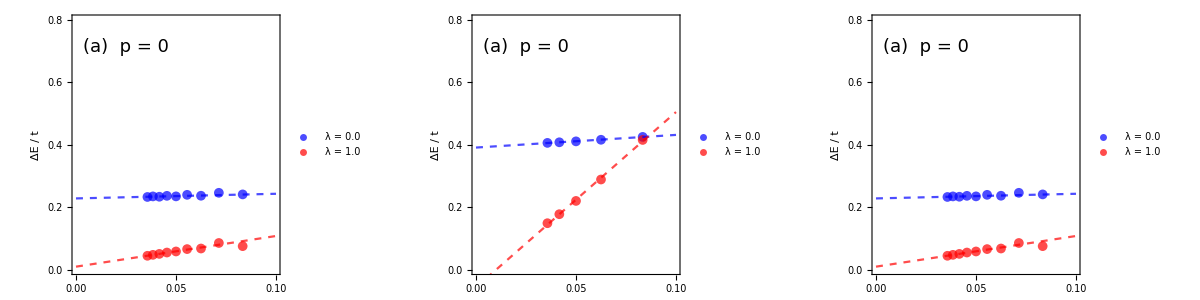

```mathematica
JRange={"0.4"};
tails={"12-2-28_0.0-1.0-1.0"};
gapPlots={};
Do[(
qpDataset=Dataset[getAssoc["qp",JRange,tail]];
qpAvail=Dataset[getStruct[qpDataset]];
Print[Style[StringJoin["J ∈ ",ToString[JRange]," @ ", tail],16]];
AppendTo[gapPlots,makePlotsGapL[]];
kDim=Length[qpAvail["momentum"]];
plots=ArrayReshape[gapPlots[[-1]],{Length[gapPlots[[-1]]]/kDim,kDim}];
Print[Grid[plots]];
),{tail,tails}]
```

```mathematica
SavePlots[]:=(
Do[(
Do[(
fileName=StringJoin["plots/scaling/gap/",
"gap_J=",ToString[qpAvail["coupling"][[iJ]]],
"_k=",ToString[qpAvail["momentum"][[ik]]],
".jpg"];
Export[fileName,gapPlots[[1,(iJ-1)*Length[qpAvail["momentum"]//Normal]+ik,1]],ImageResolution->300];
),{ik,Length[qpAvail["momentum"]//Normal]}]
),{iJ,Length[qpAvail["coupling"]//Normal]}]
)
```

```mathematica
SavePlots[]
```